```mathematica
data2=Import[NotebookDirectory[]<>"lista_menor_a_mayor(entropia).txt","Lines"];
datamat2=Import[NotebookDirectory[]<>"lista_menor_a_mayor(kolmo mat).txt","Lines"];
dataent2=Import[NotebookDirectory[]<>"lista_menor_a_mayor(kolmo secuencia).txt","Lines"];
```

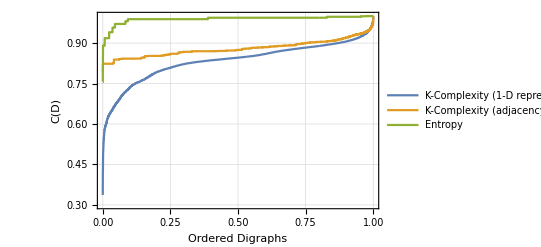

```mathematica
b2=ListLinePlot[{Rescale[data,{0,Max[data]}],Rescale[datamat,{0,Max[datamat]}],Rescale[dataent,{0,Max[dataent]}]}, PlotRange->{0.3,1},DataRange->{0,1},AxesLabel->Automatic,PlotRange->All,PlotLegends->Placed[{"K-Complexity (1-D representation)","K-Complexity (adjacency matrix)","Entropy"}, {0.45,0.25}],Frame->True,GridLines->Automatic,FrameLabel->{"Ordered Digraphs","C(D)"}]
Export[NotebookDirectory[]<>"results_ordered"<>".png",b,ImageResolution->250];
```